```mathematica
(* Use Mathematica to compute the derivatives of the fit functions wrt each parameter *)
(* R. Sheehan 19 - 10 - 2021 *)
Clear[η, Id, Is, k, T]
Vd = η k T Log[1+(Id/Is)];
D[Vd,Id]
D[Vd,η]
D[Vd, T]
D[Vd, Is]
```

(k T η)/((1+Id/Is) Is)

k T Log[1+Id/Is]

k η Log[1+Id/Is]

-(Id k T η)/((1+Id/Is) Is^2)

0.727721

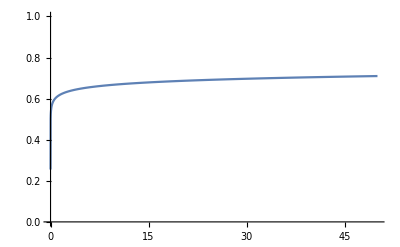

```mathematica
η=1; (* Ideality *)
T = 273.15+25; (* Temperature in K *)
k=8.61733×10^-5; (* Physical constants in J / C K *)
Is = 5000×10^-14; (* Saturation Current in mA *)
Vd/.Id->100
Plot[Vd,{Id,-0, 50},PlotRange->{{0,50},{-0,1}}]
```

```mathematica
(* look at the Lorentzian function *)
(* R. Sheehan 20 - 10 - 2021 *)
Clear[x0,Γ];
L=(Γ/2)/((x-x0)^2+(Γ/2)^2);
D[L,x]
D[L, x0]
D[L,Γ]
```

-((x-x0) Γ)/(((x-x0)^2+Γ^2/4)^2)

((x-x0) Γ)/(((x-x0)^2+Γ^2/4)^2)

-Γ^2/(4 ((x-x0)^2+Γ^2/4)^2)+1/(2 ((x-x0)^2+Γ^2/4))

```mathematica
Lor[x_,x0_,G_]:=G/((x-x0)^2+(G)^2);
```

```mathematica
Lor[80,80,2.5]//N
```

0.8

```mathematica
D[Lor[x,x0,g],g]
```

-(2 g^2)/((g^2+(x-x0)^2)^2)+1/(g^2+(x-x0)^2)

```mathematica
Clear[x0,g];
D[Lor[x,x0,g],x0]/.x->80/.x0->80/.g->1
D[Lor[x,x0,g],g]/.x->80/.x0->80/.g->1
```

0

-1

```mathematica
D[Lor[x,x0,g],g]
```

-(2 g^2)/((g^2+(x-x0)^2)^2)+1/(g^2+(x-x0)^2)

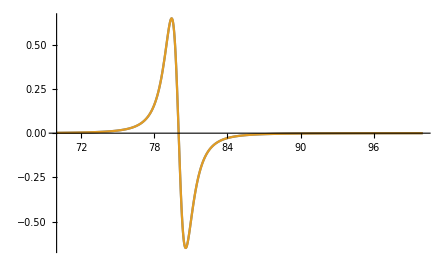

```mathematica
x0=80;
g=1;
Plot[{-((x-x0) g)/(((x-x0)^2+g^2/4)^2),-4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

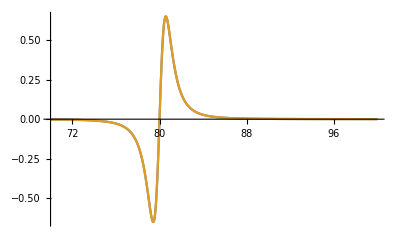

```mathematica
x0=80;
g=2;
Plot[{((x-x0) g)/(((x-x0)^2+g^2/4)^2),4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

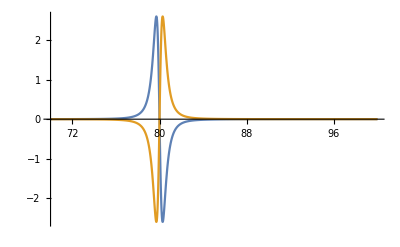

```mathematica
x0=80;
g=1;
Plot[{-4 (x-x0)1/g(Lor[x,x0,g])^2,4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

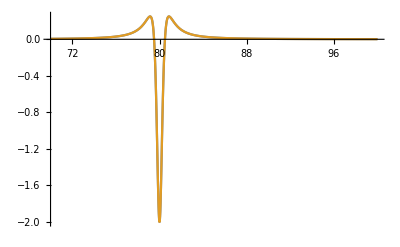

```mathematica
x0=80;
g=1;
Plot[{-g^2/(4  ((x-x0)^2+g^2/4)^2)+1/(2  ((x-x0)^2+g^2/4)),Lor[x,x0,g]/g- (Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```